# Conjecturing Theorems in Euclidean Geometry

## James Mulnix, Dan McDonald, Ian Ford, Peter Barendse, Nicolas Robles, Lin Cong WRI

Join the Conversation #WolframTechConf

## Welcome! (Init)

```mathematica
SetDirectory[NotebookDirectory[]]
<<GeometrySceneDrawer.m
<<GeometryConjectureNew.m
<<SceneExamples.m
$EntityStores={};
PrependTo[$EntityStores,EntityFramework`$SceneExample]
```

\\files\dept\DA\Geometry\PlaneGeometryDemo_Nov172017

{AffineHull,Angle,AngleBisector,CircleThrough,Collinear,Coplanar,Concurrent,Convex,Cyclic,EqualAngles,Equiangular,Equilateral,GeometricPoint,GeometricScene,InfiniteLineThrough,Inradius,LineThrough,Midpoint,Parallel,PerpendicularBisector,Radius,RegionCenter,Regular,Similar,Tangent,Unspecified,FindGeometricSceneGraphics,GeometricSceneToGraphicsPrimitives,FindGeometricCoordinates}

{FindGeometricConjectures}

{EntityFramework`$SceneExample}

Set::wrsym: Symbol $EntityStores is Protected.

{EntityStore[<>]}

```mathematica
Quiet[<<SyntheticGeometry.m]
```

```mathematica
open[thm_]:=Grid[{{"Name",thm["Label"]},{"Diagram",thm["Diagram"]},{"Statement",thm["Statement"]},{"Hypotheses",thm["Hypotheses"]},{"Conclusions",thm["Conclusions"]}},Frame->All]
```

```mathematica
conclusionVSconjecture[thm_,graph_,num__]:=
Grid[{{Text[Style["Name", Gray]],Text[Style[thm["Label"],Bold]]},
        {Text[Style["Conclusion", Gray]],thm["Conclusions"]//Column},
         {Text[Style["Conjecture",
Gray]],Column[Part[FindGeometricConjectures@graph,{num}]]}},Frame->All]
conclusionVSconjecture[thm_,num__]:=conclusionVSconjecture[thm,FindGeometricSceneGraphics[thm@"Hypotheses"],num]
```

## Overview of the Synthetic Geometry Project

We provide tools for solving problems in plane geometry using the following workflow:

### Describe Scene

Developing "scene description language" within the Wolfram Language framework to allow users to symbolically describe coordinate-free scenes in plane geometry.

Creating entity store with known theorems and accompanying information.

### Draw Scene

```mathematica
FindGeometricSceneGraphics
```

Turn scene descriptions into randomized drawings of those scenes.

Give visual representations of scenes.

Find coordinates for points that satisfy the scene.

### Make Conjectures About Scene

```mathematica
FindGeometricConjectures
```

Using coordinates returned by scene drawer, make conjectures about original abstract scene.

### Prove Theorems About Scene

Under development.

Synthetic prover: give human-readable proofs of theorems that hold given the hypotheses of the original abstract scene.

Algebraic prover: use very human-unreadable proofs to verify theorems.

## Theorem Entity Store

```mathematica
EntityValue["GeometryTheorem","Entities"]
```

{Pythagorean theorem,Pythagorean theorem converse,Thales' theorem,Archimedes' midpoint theorem,Desargues' theorem,butterfly theorem,Ceva's theorem,Ceva's theorem converse,crossed ladders theorem,Stengel's crossed ladders theorem,Ptolemy's theorem,Finsler-Hadwiger theorem,Kosnita theorem,Droz-Farny theorem,Johnson's theorem,van Aubel's theorem,Napoleon's theorem,Pappus's hexagon theorem,Morley's theorem,example 1,example 2,example 38,example 45,example 48,example 107,A Concurrency from a Point and a Triangle's Excenters,A Concurrency from Circumcircles of Subtriangles,A Concurrency from Six Pedal Points,A Concurrency from the Midpoints of Line Segments through the Circumcenter}

```mathematica
EntityProperties["GeometryTheorem"]
```

{additional people involved,alternate statements,assertions,associated entities,associated people,conclusions,constructs,diagram,eponymous people,formulation dates,formulation sources,formulators,hypotheses,label,MathWorld entry,proof dates,proof sources,provers,references,statement,variables}

```mathematica
SystemOpen@@Entity["GeometryTheorem","Finsler-HadwigerTheorem"]["MathWorld"]["URL"]
```

```mathematica
Entity["GeometryTheorem","Finsler-HadwigerTheorem"]@EntityProperty["GeometryTheorem","Diagram"]
```

-Graphics-

```mathematica
Entity["GeometryTheorem","Finsler-HadwigerTheorem"]@"Hypotheses"//Column
```

Regular[Polygon[{GeometricPoint[D],GeometricPoint[C],GeometricPoint[B],GeometricPoint[A]}]]
Regular[Polygon[{GeometricPoint[D'],GeometricPoint[C'],GeometricPoint[B'],GeometricPoint[A]}]]
Polygon[{GeometricPoint[Q],GeometricPoint[R],GeometricPoint[S],GeometricPoint[T]}]
GeometricPoint[Q]==Midpoint[LineThrough[{GeometricPoint[B'],GeometricPoint[D]}]]
GeometricPoint[S]==Midpoint[LineThrough[{GeometricPoint[B],GeometricPoint[D']}]]
GeometricPoint[R]==Midpoint[LineThrough[{GeometricPoint[A],GeometricPoint[C]}]]
GeometricPoint[T]==Midpoint[LineThrough[{GeometricPoint[A],GeometricPoint[C']}]]

```mathematica
Entity["GeometryTheorem","Finsler-HadwigerTheorem"]@"Conclusions"//Column
```

Regular[Polygon[{GeometricPoint[R],GeometricPoint[S],GeometricPoint[T],GeometricPoint[Q]}]]

## More Theorem Entity Store Examples

```mathematica
open/@Take[EntityValue["GeometryTheorem","Entities"],5]//Column
```

Name | Pythagorean theorem
Diagram | -Graphics-
Statement | For a triangle △ABC, if ∠BAC is a right angle, then BC^2 = AB^2 + AC^2.
Hypotheses | {Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Angle[GeometricPoint[B],GeometricPoint[A],GeometricPoint[C]]==90 °}
Conclusions | {EuclideanDistance[GeometricPoint[B],GeometricPoint[C]]^2==EuclideanDistance[GeometricPoint[A],GeometricPoint[B]]^2+EuclideanDistance[GeometricPoint[A],GeometricPoint[C]]^2}
Name | Pythagorean theorem converse
Diagram | -Graphics-
Statement | For a triangle △ABC, if BC^2 = AB^2 + AC^2, then ∠BAC is a right angle.
Hypotheses | {Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],EuclideanDistance[GeometricPoint[B],GeometricPoint[C]]^2==EuclideanDistance[GeometricPoint[A],GeometricPoint[B]]^2+EuclideanDistance[GeometricPoint[A],GeometricPoint[C]]^2}
Conclusions | {Angle[GeometricPoint[B],GeometricPoint[A],GeometricPoint[C]]==90 °}
Name | Thales' theorem
Diagram | -Graphics-
Statement | If A, B and C are points on a circle where the line [AC] is a diameter of the circle, then the angle ∠ABC is a right angle.
Hypotheses | {CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]},GeometricPoint[O]],Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[O]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[C]}]]}
Conclusions | {Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]]==90 °}
Name | Archimedes' midpoint theorem
Diagram | -Graphics-
Statement | Let M be the midpoint of the arc AMB. Pick C at random and pick D such that (MD) ⊥ (AC). Then |AD| = |DC| + |BC|.
Hypotheses | {CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[M]}],EuclideanDistance[GeometricPoint[A],GeometricPoint[M]]==EuclideanDistance[GeometricPoint[B],GeometricPoint[M]],LineThrough[{GeometricPoint[B],GeometricPoint[C]}],LineThrough[{GeometricPoint[M],GeometricPoint[D]}]⊥LineThrough[{GeometricPoint[A],GeometricPoint[D],GeometricPoint[C]}]}
Conclusions | {EuclideanDistance[GeometricPoint[A],GeometricPoint[D]]==EuclideanDistance[GeometricPoint[B],GeometricPoint[C]]+EuclideanDistance[GeometricPoint[D],GeometricPoint[C]]}
Name | Desargues' theorem
Diagram | -Graphics-
Statement | If the three straight lines joining the corresponding vertices of two triangles ABC and A'B'C' all meet in a point (the perspector), then the three intersections of pairs of corresponding sides lie on a straight line (the perspectrix). Equivalently, if two triangles are perspective from a point, they are perspective from a line.
Hypotheses | {Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Triangle[{GeometricPoint[A'],GeometricPoint[B'],GeometricPoint[C']}],InfiniteLineThrough[{GeometricPoint[O],GeometricPoint[A],GeometricPoint[A']}],InfiniteLineThrough[{GeometricPoint[O],GeometricPoint[B],GeometricPoint[B']}],InfiniteLineThrough[{GeometricPoint[O],GeometricPoint[C],GeometricPoint[C']}],InfiniteLineThrough[{GeometricPoint[R],GeometricPoint[A],GeometricPoint[B]}],InfiniteLineThrough[{GeometricPoint[R],GeometricPoint[A'],GeometricPoint[B']}],InfiniteLineThrough[{GeometricPoint[S],GeometricPoint[A],GeometricPoint[C]}],InfiniteLineThrough[{GeometricPoint[S],GeometricPoint[A'],GeometricPoint[C']}],InfiniteLineThrough[{GeometricPoint[T],GeometricPoint[B],GeometricPoint[C]}],InfiniteLineThrough[{GeometricPoint[T],GeometricPoint[B'],GeometricPoint[C']}]}
Conclusions | {Collinear[GeometricPoint[R],GeometricPoint[S],GeometricPoint[T]]}

## Thales’ theorem

```mathematica
Entity["GeometryTheorem","ThalesTheorem"]@"Diagram"
```

-Graphics-

```mathematica
(hyp=Entity["GeometryTheorem","ThalesTheorem"]@"Hypotheses")//Column
```

CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]},GeometricPoint[O]]
Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}]
GeometricPoint[O]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[C]}]]

```mathematica
Entity["GeometryTheorem","ThalesTheorem"]@"Conclusions"//Column
```

Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]]==90 °

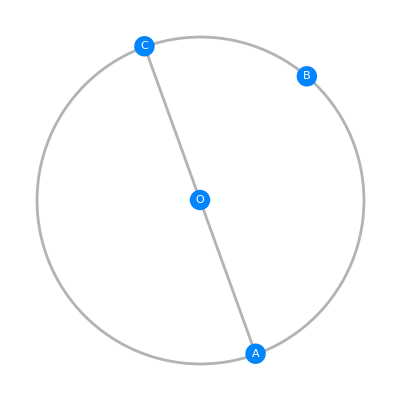

```mathematica
graph=FindGeometricSceneGraphics[hyp]
```

```mathematica
thalesCoords=FindGeometricCoordinates@hyp
```

{GeometricPoint[A]→{1.7045,2.97073},GeometricPoint[C]→{1.70121,-0.0143357},GeometricPoint[B]→{0.375205,2.16011},Unspecified[ref,{1,0},1]→{2.91694,2.34634},Unspecified[ref,{1,0},2]→{0.728172,2.60853},Unspecified[ref,{1,0},3]→{1.13717,2.85938},GeometricPoint[O]→{1.70286,1.4782}}

```mathematica
thalesPrims=GeometricSceneToGraphicsPrimitives@hyp
```

{AbsoluteThickness[2],{{Opacity[0],EdgeForm[{GrayLevel[0.7],Thickness[Medium]}],Polygon[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}]},{GrayLevel[0.7],Line[{GeometricPoint[A],GeometricPoint[C]}]},{GrayLevel[0.7],Circle[GeometricPoint[O],1/6 (EuclideanDistance[GeometricPoint[O],GeometricPoint[A]]+EuclideanDistance[GeometricPoint[O],GeometricPoint[B]]+EuclideanDistance[GeometricPoint[O],GeometricPoint[C]]+EuclideanDistance[GeometricPoint[O],Unspecified[ref,{1,0},1]]+EuclideanDistance[GeometricPoint[O],Unspecified[ref,{1,0},2]]+EuclideanDistance[GeometricPoint[O],Unspecified[ref,{1,0},3]])]}},{Inset[-Graphics-,GeometricPoint[A]],Inset[A,GeometricPoint[A]],Inset[-Graphics-,GeometricPoint[B]],Inset[B,GeometricPoint[B]],Inset[-Graphics-,GeometricPoint[C]],Inset[C,GeometricPoint[C]],Inset[-Graphics-,GeometricPoint[O]],Inset[O,GeometricPoint[O]]}}

```mathematica
graph//FullForm
```

Annotation[Graphics[List[AbsoluteThickness[2],List[List[Opacity[0],EdgeForm[List[GrayLevel[0.7],Thickness[Medium]]],Polygon[List[List[1.65545,-0.949002],List[2.31336,2.60859],List[0.230504,2.99378]]]],List[GrayLevel[0.7],Line[List[List[1.65545,-0.949002],List[0.230504,2.99378]]]],List[GrayLevel[0.7],Circle[List[0.942977,1.02239],2.09619]]],List[Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],List[1.65545,-0.949002]],Inset[Style["A",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],List[1.65545,-0.949002]],Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],List[2.31336,2.60859]],Inset[Style["B",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],List[2.31336,2.60859]],Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],List[0.230504,2.99378]],Inset[Style["C",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],List[0.230504,2.99378]],Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],List[0.942977,1.02239]],Inset[Style["O",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],List[0.942977,1.02239]]]]],Association[Rule["sceneList",List[CircleThrough[List[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]],GeometricPoint["O"]],Triangle[List[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]]],Equal[GeometricPoint["O"],Midpoint[Line[List[GeometricPoint["A"],GeometricPoint["C"]]]]]]],Rule["sceneAssociation",Association[Rule["invisibleLines",List[]],Rule["isolatedPoints",List[GeometricPoint["O"]]],Rule["constraints",List[True,Equal[List[GeometricPoint["O"][1],GeometricPoint["O"][2]],List[Times[Rational[1,2],Plus[GeometricPoint["A"][1],GeometricPoint["C"][1]]],Times[Rational[1,2],Plus[GeometricPoint["A"][2],GeometricPoint["C"][2]]]]]]],Rule["lines",List[List[GeometricPoint["A"],GeometricPoint["C"]]]],Rule["infiniteLines",List[]],Rule["circles",List[List[List[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],Unspecified["ref",List[1,0],1],Unspecified["ref",List[1,0],2],Unspecified["ref",List[1,0],3]],GeometricPoint["O"]]]],Rule["disks",List[]],Rule["angleRules",List[]],Rule["nonintersectingSegments",List[]],Rule["polygons",List[]],Rule["nonintersectingPolygons",List[]],Rule["counterclockwisePolygons",List[]],Rule["convexPolygons",List[List[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]]]],Rule["equiangularPolygons",List[]],Rule["equilateralPolygons",List[]],Rule["regularPolygons",List[]],Rule["quantities",List[]],Rule["midpointTriples",List[List[GeometricPoint["A"],GeometricPoint["O"],GeometricPoint["C"]]]],Rule["invisiblePoints",List[Unspecified["ref",List[1,0],1],Unspecified["ref",List[1,0],2],Unspecified["ref",List[1,0],3]]]]],Rule["primitives",List[AbsoluteThickness[2],List[List[Opacity[0],EdgeForm[List[GrayLevel[0.7],Thickness[Medium]]],Polygon[List[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]]]],List[GrayLevel[0.7],Line[List[GeometricPoint["A"],GeometricPoint["C"]]]],List[GrayLevel[0.7],Circle[GeometricPoint["O"],Times[Rational[1,6],Plus[EuclideanDistance[GeometricPoint["O"],GeometricPoint["A"]],EuclideanDistance[GeometricPoint["O"],GeometricPoint["B"]],EuclideanDistance[GeometricPoint["O"],GeometricPoint["C"]],EuclideanDistance[GeometricPoint["O"],Unspecified["ref",List[1,0],1]],EuclideanDistance[GeometricPoint["O"],Unspecified["ref",List[1,0],2]],EuclideanDistance[GeometricPoint["O"],Unspecified["ref",List[1,0],3]]]]]]],List[Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],GeometricPoint["A"]],Inset[Style["A",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],GeometricPoint["A"]],Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],GeometricPoint["B"]],Inset[Style["B",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],GeometricPoint["B"]],Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],GeometricPoint["C"]],Inset[Style["C",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],GeometricPoint["C"]],Inset[Graphics[List[Hue[0.58,1,1,1],Disk[List[0,0]]],Rule[ImageSize,21]],GeometricPoint["O"]],Inset[Style["O",Rule[LineColor,RGBColor[0,0,1]],Rule[FrontFaceColor,RGBColor[0,0,1]],Rule[BackFaceColor,RGBColor[0,0,1]],Rule[GraphicsColor,RGBColor[0,0,1]],Rule[FontSize,Medium],Rule[FontColor,GrayLevel[1]]],GeometricPoint["O"]]]]],Rule["coordinates",List[Rule[GeometricPoint["A"],List[1.65545,-0.949002]],Rule[GeometricPoint["C"],List[0.230504,2.99378]],Rule[GeometricPoint["B"],List[2.31336,2.60859]],Rule[Unspecified["ref",List[1,0],1],List[3.03297,1.18344]],Rule[Unspecified["ref",List[1,0],2],List[2.77267,-0.000452819]],Rule[Unspecified["ref",List[1,0],3],List[2.77958,0.0119974]],Rule[GeometricPoint["O"],List[0.942977,1.02239]]]]]]

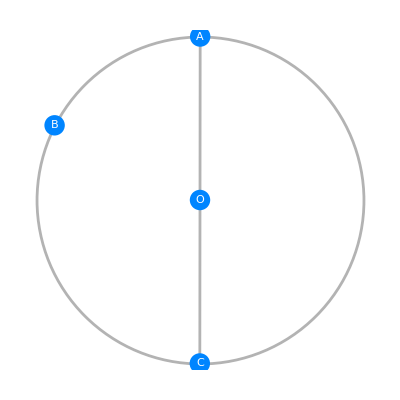

```mathematica
Graphics[thalesPrims/.thalesCoords]
```

```mathematica
FindGeometricConjectures[graph]//Column
```

Line[{GeometricPoint[A],GeometricPoint[B]}]⊥Line[{GeometricPoint[C],GeometricPoint[B]}]
Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]]==90 °

```mathematica
FindGeometricConjectures[graph,Infinity,"Diagram"]
```

12

```mathematica
conclusionVSconjecture[Entity["GeometryTheorem","ThalesTheorem"],graph,2]
```

Name | Thales' theorem
Conclusion | Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]]==90 °
Conjecture | Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]]==90 °

```mathematica
FindGeometricConjectures[hyp]//Column
```

Line[{GeometricPoint[C],GeometricPoint[B]}]⊥Line[{GeometricPoint[B],GeometricPoint[A]}]
Angle[GeometricPoint[C],GeometricPoint[B],GeometricPoint[A]]==90 °

```mathematica
FindGeometricConjectures[hyp,Infinity,"Diagram"]
```

12

## Butterfly theorem

```mathematica
Entity["GeometryTheorem","ButterflyTheorem"]@"Diagram"
```

-Graphics-

```mathematica
(hypB=Entity["GeometryTheorem","ButterflyTheorem"]@"Hypotheses")//Column
```

CircleThrough[{GeometricPoint[A],GeometricPoint[P],GeometricPoint[D],GeometricPoint[B],GeometricPoint[Q],GeometricPoint[C]}]
GeometricPoint[M]==Midpoint[Line[{GeometricPoint[P],GeometricPoint[Q]}]]
LineThrough[{GeometricPoint[A],GeometricPoint[M],GeometricPoint[B]}]
LineThrough[{GeometricPoint[C],GeometricPoint[M],GeometricPoint[D]}]
LineThrough[{GeometricPoint[P],GeometricPoint[X],GeometricPoint[Q]}]
LineThrough[{GeometricPoint[A],GeometricPoint[X],GeometricPoint[D]}]
LineThrough[{GeometricPoint[P],GeometricPoint[Y],GeometricPoint[Q]}]
LineThrough[{GeometricPoint[B],GeometricPoint[Y],GeometricPoint[C]}]

```mathematica
Entity["GeometryTheorem","ButterflyTheorem"]@"Conclusions"//Column
```

GeometricPoint[M]==Midpoint[Line[{GeometricPoint[X],GeometricPoint[Y]}]]

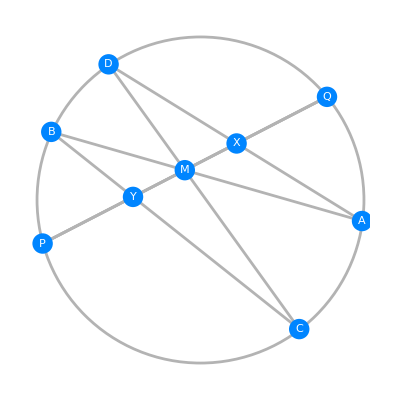

```mathematica
graphB=FindGeometricSceneGraphics[hypB]
```

```mathematica
FindGeometricConjectures[graphB,Infinity,"Language"]//Length
```

32

```mathematica
FindGeometricConjectures[graphB,10,"Diagram"]
```

12345678910

```mathematica
conclusionVSconjecture[Entity["GeometryTheorem","ButterflyTheorem"],graphB,2]
```

Name | butterfly theorem
Conclusion | GeometricPoint[M]==Midpoint[Line[{GeometricPoint[X],GeometricPoint[Y]}]]
Conjecture | GeometricPoint[M]==Midpoint[Line[{GeometricPoint[Y],GeometricPoint[X]}]]

## Pappus’s Hexagon theorem

```mathematica
Entity["GeometryTheorem","PappussHexagonTheorem"]@"Diagram"
```

-Graphics-

```mathematica
(hypP=Entity["GeometryTheorem","PappussHexagonTheorem"]@"Hypotheses")//Column
```

LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}]
LineThrough[{GeometricPoint[D],GeometricPoint[E],GeometricPoint[F]}]
LineThrough[{GeometricPoint[A],GeometricPoint[X],GeometricPoint[E]}]
LineThrough[{GeometricPoint[B],GeometricPoint[X],GeometricPoint[D]}]
LineThrough[{GeometricPoint[A],GeometricPoint[Y],GeometricPoint[F]}]
LineThrough[{GeometricPoint[C],GeometricPoint[Y],GeometricPoint[D]}]
LineThrough[{GeometricPoint[B],GeometricPoint[Z],GeometricPoint[F]}]
LineThrough[{GeometricPoint[C],GeometricPoint[Z],GeometricPoint[E]}]
InfiniteLineThrough[{GeometricPoint[X],GeometricPoint[Z]}]

```mathematica
Entity["GeometryTheorem","PappussHexagonTheorem"]@"Conclusions"//Column
```

Collinear[GeometricPoint[X],GeometricPoint[Y],GeometricPoint[Z]]

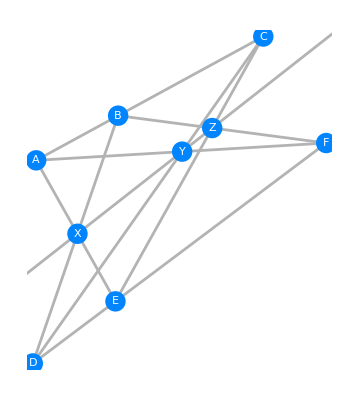

```mathematica
graphP=FindGeometricSceneGraphics[hypP]
```

```mathematica
FindGeometricConjectures[graphP,5]//Column
```

Collinear[GeometricPoint[Z],GeometricPoint[Y],GeometricPoint[X]]
Angle[GeometricPoint[D],GeometricPoint[X],GeometricPoint[E]]==Angle[GeometricPoint[B],GeometricPoint[X],GeometricPoint[A]]
Angle[GeometricPoint[D],GeometricPoint[X],GeometricPoint[A]]==Angle[GeometricPoint[B],GeometricPoint[X],GeometricPoint[E]]
Angle[GeometricPoint[D],GeometricPoint[Y],GeometricPoint[F]]==Angle[GeometricPoint[C],GeometricPoint[Y],GeometricPoint[A]]
Angle[GeometricPoint[D],GeometricPoint[Y],GeometricPoint[A]]==Angle[GeometricPoint[C],GeometricPoint[Y],GeometricPoint[F]]

```mathematica
FindGeometricConjectures[graphP,Infinity,"Diagram"]
```

1234567

```mathematica
conclusionVSconjecture[Entity["GeometryTheorem","PappussHexagonTheorem"],graphP,1]
```

Name | Pappus's hexagon theorem
Conclusion | Collinear[GeometricPoint[X],GeometricPoint[Y],GeometricPoint[Z]]
Conjecture | Collinear[GeometricPoint[Z],GeometricPoint[Y],GeometricPoint[X]]

## Finsler-Hadwiger theorem

```mathematica
Entity["GeometryTheorem","Finsler-HadwigerTheorem"]@"Diagram"
```

-Graphics-

```mathematica
(hypF=Entity["GeometryTheorem","Finsler-HadwigerTheorem"]@"Hypotheses")//Column
```

Regular[Polygon[{GeometricPoint[D],GeometricPoint[C],GeometricPoint[B],GeometricPoint[A]}]]
Regular[Polygon[{GeometricPoint[D'],GeometricPoint[C'],GeometricPoint[B'],GeometricPoint[A]}]]
Polygon[{GeometricPoint[Q],GeometricPoint[R],GeometricPoint[S],GeometricPoint[T]}]
GeometricPoint[Q]==Midpoint[LineThrough[{GeometricPoint[B'],GeometricPoint[D]}]]
GeometricPoint[S]==Midpoint[LineThrough[{GeometricPoint[B],GeometricPoint[D']}]]
GeometricPoint[R]==Midpoint[LineThrough[{GeometricPoint[A],GeometricPoint[C]}]]
GeometricPoint[T]==Midpoint[LineThrough[{GeometricPoint[A],GeometricPoint[C']}]]

```mathematica
Entity["GeometryTheorem","Finsler-HadwigerTheorem"]@"Conclusions"//Column
```

Regular[Polygon[{GeometricPoint[R],GeometricPoint[S],GeometricPoint[T],GeometricPoint[Q]}]]

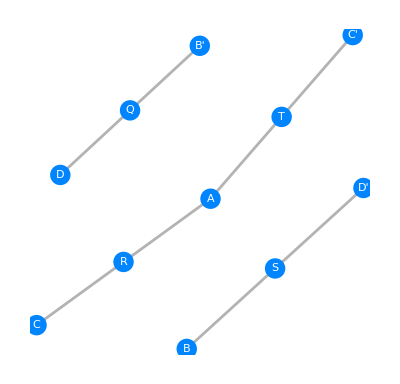

```mathematica
graphF=FindGeometricSceneGraphics[hypF]
```

```mathematica
FindGeometricConjectures[graphF]//Length
```

31

```mathematica
FindGeometricConjectures[graphF,5,"Diagram"]
```

12345

```mathematica
conclusionVSconjecture[Entity["GeometryTheorem","Finsler-HadwigerTheorem"],graphF,1]
```

Name | Finsler-Hadwiger theorem
Conclusion | Regular[Polygon[{GeometricPoint[R],GeometricPoint[S],GeometricPoint[T],GeometricPoint[Q]}]]
Conjecture | Regular[Polygon[{GeometricPoint[Q],GeometricPoint[T],GeometricPoint[S],GeometricPoint[R]}]]

## Kosnita theorem

```mathematica
Entity["GeometryTheorem","KosnitaTheorem"]@"Diagram"
```

-Graphics-

```mathematica
(hypK=Entity["GeometryTheorem","KosnitaTheorem"]@"Hypotheses")//Column
```

GeometricPoint[O]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Circumcenter]
GeometricPoint[Obco]==RegionCenter[Triangle[{GeometricPoint[O],GeometricPoint[B],GeometricPoint[C]}],Circumcenter]
GeometricPoint[Ocao]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[O],GeometricPoint[C]}],Circumcenter]
GeometricPoint[Oabo]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[O]}],Circumcenter]
InfiniteLineThrough[{GeometricPoint[A],GeometricPoint[Obco]}]
InfiniteLineThrough[{GeometricPoint[B],GeometricPoint[Ocao]}]
InfiniteLineThrough[{GeometricPoint[C],GeometricPoint[Oabo]}]

```mathematica
Entity["GeometryTheorem","KosnitaTheorem"]@"Conclusions"//Column
```

Concurrent[Line[{GeometricPoint[A],GeometricPoint[Obco]}],Line[{GeometricPoint[B],GeometricPoint[Ocao]}],Line[{GeometricPoint[C],GeometricPoint[Oabo]}]]

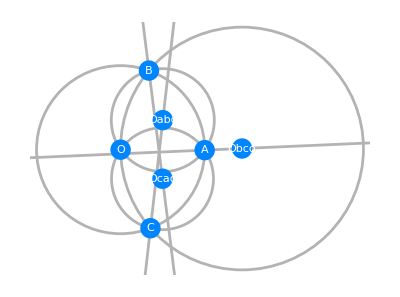

```mathematica
graphK=FindGeometricSceneGraphics[hypK]
```

```mathematica
FindGeometricConjectures[graphK,Infinity,"Diagram"]
```

12345678

```mathematica
conclusionVSconjecture[Entity["GeometryTheorem","KosnitaTheorem"],graphK,1]
```

Name | Kosnita theorem
Conclusion | Concurrent[Line[{GeometricPoint[A],GeometricPoint[Obco]}],Line[{GeometricPoint[B],GeometricPoint[Ocao]}],Line[{GeometricPoint[C],GeometricPoint[Oabo]}]]
Conjecture | Concurrent[Line[{GeometricPoint[A],GeometricPoint[Obco]}],Line[{GeometricPoint[B],GeometricPoint[Ocao]}],Line[{GeometricPoint[C],GeometricPoint[Oabo]}]]

## Synthetic geometry prover

We demonstrate a geometry prover currently in development.

Target: elementary (9th grade) geometry proofs (deriving lengths, angles, areas, etc from known values)

Presentation: two-column proof (facts and their justifications)

Method: start with given facts, and apply theorems to deduce everything you can

## Elementary angle example

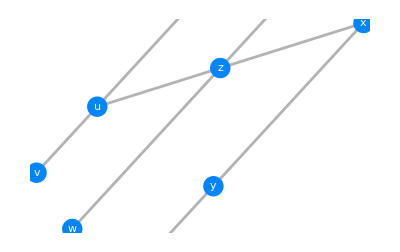

```mathematica
AngleScene1={
Parallel[
InfiniteLineThrough[{GeometricPoint["x"],GeometricPoint["y"]}],
InfiniteLineThrough[{GeometricPoint["z"],GeometricPoint["w"]}],
InfiniteLineThrough[{GeometricPoint["u"],GeometricPoint["v"]}]
],
InfiniteLineThrough[{GeometricPoint["x"],GeometricPoint["z"],GeometricPoint["u"]}],
Angle[GeometricPoint["y"],GeometricPoint["x"],GeometricPoint["z"]]==30
};
```

```mathematica
AngleScene1//Column//GeometricTraditionalForm
```

||  || xyzwuv
xzu
∠yxz == 30

```mathematica
ProveGeometricFacts[AngleScene1]["TwoColumnProof"]//TraditionalForm
```

Fact | Reason
 ||  || xyzwuv | given
  xzuis a line | given
∠yxz == 30 | given
∠yxu == 30 | Since xzu are on a line, angle ∠yxu is just the angle ∠yxz by another name, which is 30 degrees
∠xzw == 150 | Since xy and zw are parallel lines, ∠xzw is the supplement of ∠yxz
∠wzu == 30 | ∠wzu is the supplement angle to ∠xzw, which is 150 degrees
∠xuv == 150 | Since xy and uv are parallel lines, ∠xuv is the supplement of ∠yxu
∠zuv == 150 | Since xzu are on a line, angle ∠zuv is just the angle ∠xuv by another name, which is 150 degrees

## Length & area example

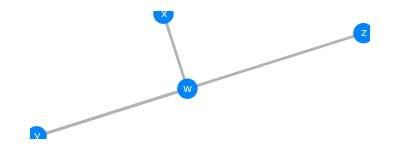

```mathematica
TriangleScene1={
Parallel@InfiniteLineThrough[{GeometricPoint["y"],GeometricPoint["w"],GeometricPoint["z"]}],
EuclideanDistance[GeometricPoint["x"],GeometricPoint["w"]]==3,
EuclideanDistance[GeometricPoint["y"],GeometricPoint["w"]]==6,
EuclideanDistance[GeometricPoint["w"],GeometricPoint["z"]]==7,
Angle[GeometricPoint["y"],GeometricPoint["w"],GeometricPoint["x"]]==90
};
```

```mathematica
TriangleScene1//Column//GeometricTraditionalForm
```

ywzis a line
distance(x, w) == 3
distance(y, w) == 6
distance(w, z) == 7
∠ywx == 90

```mathematica
TriangleProof1=ProveGeometricFacts[
GeometricScene@TriangleScene1,
fixedthms,
"TargetFact"->HoldPattern[GeometricArea[{GeometricPoint["y"],GeometricPoint["z"],GeometricPoint["x"]}]]==_
];
```

```mathematica
TriangleProof1["TwoColumnProof"]//TraditionalForm
```

Fact | Reason
  ywzis a line | given
distance(w, x) == 3 | given
distance(w, y) == 6 | given
distance(w, z) == 7 | given
∠ywx == 90 | given
distance(y, z) == 13 | Since distance(w, y) == 6, distance(w, z) == 7, and the fact that y, w, and z lie on a line (in that order)
∠xwz == 90 | ∠xwz is the supplement angle to ∠ywx, which is 90 degrees
area(Δyzx) == 39/2 | Since distance(y, z) == 13, and distance(w, x) == 3 is a (perpendicular) altitude/height of this triangle, area(Δyzx) == 39/2

```mathematica
TriangleProof1["ProofNetwork"]
```

## Thales theorem

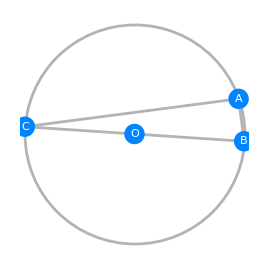

```mathematica
ThalesScene1 = {
CircleThrough[{GeometricPoint["B"],GeometricPoint["A"],GeometricPoint["C"]},GeometricPoint["O"],r],
InfiniteLineThrough[{GeometricPoint["B"],GeometricPoint["O"],GeometricPoint["C"]}],
(*needed for 'seeding' *)
Angle[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]]==b,
Angle[GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["A"]]==c
};
```

```mathematica
ThalesScene1//Column//GeometricTraditionalForm
```

circle with center O of radius r with points {B,A,C}
BOC
∠ABC == b
∠BCA == c

#### First attempt

By default ProveGeometricFacts proves everything it can about the scene. For the Thales scene, the prover does find the conclusion, along with 50+ other facts.

(*Warning: This is time-consuming*)

```mathematica
ThalesProof1=ProveGeometricFacts[ThalesScene1];
```

```mathematica
ThalesProof1["TwoColumnProof"]//TraditionalForm
```

Fact | Reason
circle with center O of radius r with points {B,A,C} | given
  BOCis a line | given
∠ABC == b | given
∠BCA == c | given
∠CAB == -b-c+180 | Since ∠BCA == c degrees and ∠ABC == b degrees, ∠CAB == 180-b-c degrees because these form a triangle
∠OCA == c | Since BOC are on a line, angle ∠OCA is just the angle ∠BCA by another name, which is c degrees
∠ABO == b | Since BOC are on a line, angle ∠ABO is just the angle ∠ABC by another name, which is b degrees
distance(A, O) == r | Since A is a point on the circle and radius r centered at O, distance(A, O) == r
distance(C, O) == r | Since C is a point on the circle and radius r centered at O, distance(C, O) == r
distance(B, O) == r | Since B is a point on the circle and radius r centered at O, distance(B, O) == r
distance(A, O) == distance(C, O)
distance(B, O) == distance(C, O)
∠ABC == ∠ABO
∠BCA == ∠OCA | by algebra on :
∠ABC == b
∠BCA == c
∠CAB == -b-c+180
∠OCA == c
∠ABO == b
distance(A, O) == r
distance(C, O) == r
distance(B, O) == r
distance(B, C) == 2 r | Since distance(B, O) == r, distance(C, O) == r, and the fact that B, O, and C lie on a line (in that order)
∠CAB == -b-∠OCA+180 | Since ∠BCA == ∠OCA degrees and ∠ABC == b degrees, ∠CAB == 180-∠OCA-b degrees because these form a triangle
∠CAB == -c-∠ABO+180 | Since ∠ABC == ∠ABO degrees and ∠BCA == c degrees, ∠CAB == 180-∠ABO-c degrees because these form a triangle
∠CAB == -∠ABO-∠OCA+180 | Since ∠BCA == ∠OCA degrees and ∠ABC == ∠ABO degrees, ∠CAB == 180-∠ABO-∠OCA degrees because these form a triangle
∠OAB == ∠ABO | angles opposite equal sides of an isoceles triangle are also equal
∠CAO == ∠OCA | angles opposite equal sides of an isoceles triangle are also equal
∠CBO == ∠OCB | angles opposite equal sides of an isoceles triangle are also equal
∠ABC == ∠OAB
∠BCA == ∠CAO | by algebra on :
∠ABC == b
∠BCA == c
∠CAB == -b-c+180
∠OCA == c
∠ABO == b
∠ABC == ∠ABO
∠BCA == ∠OCA
∠CAB == -b-∠OCA+180
∠CAB == -c-∠ABO+180
∠CAB == -∠ABO-∠OCA+180
∠OAB == ∠ABO
∠CAO == ∠OCA
∠CBO == ∠OCB
distance(C, O) == 2 r-distance(C, O) | Since distance(B, C) == 2 r, distance(B, O) == distance(C, O), and the fact that B, O, and C lie on a line (in that order)
∠BOA == -b-∠ABO+180 | Since ∠OAB == ∠ABO degrees and ∠ABO == b degrees, ∠BOA == 180-∠ABO-b degrees because these form a triangle
∠AOC == -c-∠OCA+180 | Since ∠OCA == c degrees and ∠CAO == ∠OCA degrees, ∠AOC == 180-∠OCA-c degrees because these form a triangle
distance(B, O) == distance(C, O) | Since distance(B, C) == 2 r, distance(C, O) == Plus[Times[-1, distance(C, O)], Times[2, r]], and the fact that B, O, and C lie on a line (in that order)
∠BOA == c+∠OCA | ∠BOA is the supplement angle to ∠AOC, which is 180-∠OCA-c degrees
∠AOC == b+∠ABO | ∠AOC is the supplement angle to ∠BOA, which is 180-∠ABO-b degrees
∠ABC == 1/2 (-c-∠OCA+180) | Since inscribed angles subtending the same circular arc as a central angle measure half of the central angle, ∠ABC = (∠AOC/2) = 1/2 (180-∠OCA-c).
∠BCA == 1/2 (-b-∠ABO+180) | Since inscribed angles subtending the same circular arc as a central angle measure half of the central angle, ∠BCA = (∠BOA/2) = 1/2 (180-∠ABO-b).
arc of the circle with center O from A to C has length  == 1/180 π r (-c-∠OCA+180) | Since the arc length along a circle is equal to the radius times the central angle subtending the arc (in radians), the arc length from A to C is 180-∠OCA-c × r × (π/180) = 1/180 (180-∠OCA-c) π r
arc of the circle with center O from B to A has length  == 1/180 π r (-b-∠ABO+180) | Since the arc length along a circle is equal to the radius times the central angle subtending the arc (in radians), the arc length from B to A is 180-∠ABO-b × r × (π/180) = 1/180 (180-∠ABO-b) π r
∠OCA == 1/2 (-b-∠ABO+180) | Since BOC are on a line, angle ∠OCA is just the angle ∠BCA by another name, which is 1/2 (-b-∠ABO+180) degrees
∠ABO == 1/2 (-c-∠OCA+180) | Since BOC are on a line, angle ∠ABO is just the angle ∠ABC by another name, which is 1/2 (-c-∠OCA+180) degrees
∠ABC == (b+∠ABO)/2 | Since inscribed angles subtending the same circular arc as a central angle measure half of the central angle, ∠ABC = (∠AOC/2) = (∠ABO+b)/2.
∠BCA == (c+∠OCA)/2 | Since inscribed angles subtending the same circular arc as a central angle measure half of the central angle, ∠BCA = (∠BOA/2) = (∠OCA+c)/2.
arc of the circle with center O from A to C has length  == 1/180 π r (b+∠ABO) | Since the arc length along a circle is equal to the radius times the central angle subtending the arc (in radians), the arc length from A to C is ∠ABO+b × r × (π/180) = 1/180 (∠ABO+b) π r
arc of the circle with center O from B to A has length  == 1/180 π r (c+∠OCA) | Since the arc length along a circle is equal to the radius times the central angle subtending the arc (in radians), the arc length from B to A is ∠OCA+c × r × (π/180) = 1/180 (∠OCA+c) π r
∠CAB == 90 | by algebra on :
∠ABC == b
∠BCA == c
∠CAB == -b-c+180
∠OCA == c
∠ABO == b
∠ABC == ∠ABO
∠BCA == ∠OCA
∠CAB == -b-∠OCA+180
∠CAB == -c-∠ABO+180
∠CAB == -∠ABO-∠OCA+180
∠OAB == ∠ABO
∠CAO == ∠OCA
∠CBO == ∠OCB
∠ABC == ∠OAB
∠BCA == ∠CAO
∠BOA == -b-∠ABO+180
∠AOC == -c-∠OCA+180
∠BOA == c+∠OCA
∠AOC == b+∠ABO
∠ABC == 1/2 (-c-∠OCA+180)
∠BCA == 1/2 (-b-∠ABO+180)
∠OCA == 1/2 (-b-∠ABO+180)
∠ABO == 1/2 (-c-∠OCA+180)
∠ABC == (b+∠ABO)/2
∠BCA == (c+∠OCA)/2
∠CAB == 1/2 (b+∠ABO-180)-b+180 | Since ∠BCA == 1/2 (180-∠ABO-b) degrees and ∠ABC == b degrees, ∠CAB == 180-b+1/2 (-180+∠ABO+b) degrees because these form a triangle
∠CAB == -b+1/2 (-c-∠OCA)+180 | Since ∠BCA == (∠OCA+c)/2 degrees and ∠ABC == b degrees, ∠CAB == 180-b+1/2 (-∠OCA-c) degrees because these form a triangle
∠CAB == -b-∠CAO+180 | Since ∠BCA == ∠CAO degrees and ∠ABC == b degrees, ∠CAB == 180-∠CAO-b degrees because these form a triangle
∠CAB == 1/2 (-b-∠ABO)-c+180 | Since ∠BCA == c degrees and ∠ABC == (∠ABO+b)/2 degrees, ∠CAB == 180+1/2 (-∠ABO-b)-c degrees because these form a triangle
∠CAB == 1/2 (-b-∠ABO)+1/2 (b+∠ABO-180)+180 | Since ∠BCA == 1/2 (180-∠ABO-b) degrees and ∠ABC == (∠ABO+b)/2 degrees, ∠CAB == 180+1/2 (-∠ABO-b)+1/2 (-180+∠ABO+b) degrees because these form a triangle
∠CAB == 1/2 (-b-∠ABO)+1/2 (-c-∠OCA)+180 | Since ∠BCA == (∠OCA+c)/2 degrees and ∠ABC == (∠ABO+b)/2 degrees, ∠CAB == 180+1/2 (-∠ABO-b)+1/2 (-∠OCA-c) degrees because these form a triangle
∠CAB == 1/2 (-b-∠ABO)-∠CAO+180 | Since ∠BCA == ∠CAO degrees and ∠ABC == (∠ABO+b)/2 degrees, ∠CAB == 180-∠CAO+1/2 (-∠ABO-b) degrees because these form a triangle
∠CAB == 1/2 (-b-∠ABO)-∠OCA+180 | Since ∠BCA == ∠OCA degrees and ∠ABC == (∠ABO+b)/2 degrees, ∠CAB == 180-∠OCA+1/2 (-∠ABO-b) degrees because these form a triangle
∠CAB == 1/2 (c+∠OCA-180)-c+180 | Since ∠BCA == c degrees and ∠ABC == 1/2 (180-∠OCA-c) degrees, ∠CAB == 180-c+1/2 (-180+∠OCA+c) degrees because these form a triangle
∠CAB == 1/2 (b+∠ABO-180)+1/2 (c+∠OCA-180)+180 | Since ∠BCA == 1/2 (180-∠ABO-b) degrees and ∠ABC == 1/2 (180-∠OCA-c) degrees, ∠CAB == 180+1/2 (-180+∠ABO+b)+1/2 (-180+∠OCA+c) degrees because these form a triangle
∠CAB == 1/2 (-c-∠OCA)+1/2 (c+∠OCA-180)+180 | Since ∠BCA == (∠OCA+c)/2 degrees and ∠ABC == 1/2 (180-∠OCA-c) degrees, ∠CAB == 180+1/2 (-∠OCA-c)+1/2 (-180+∠OCA+c) degrees because these form a triangle
∠CAB == 1/2 (c+∠OCA-180)-∠CAO+180 | Since ∠BCA == ∠CAO degrees and ∠ABC == 1/2 (180-∠OCA-c) degrees, ∠CAB == 180-∠CAO+1/2 (-180+∠OCA+c) degrees because these form a triangle
∠CAB == 1/2 (c+∠OCA-180)-∠OCA+180 | Since ∠BCA == ∠OCA degrees and ∠ABC == 1/2 (180-∠OCA-c) degrees, ∠CAB == 180-∠OCA+1/2 (-180+∠OCA+c) degrees because these form a triangle
∠CAB == -c-∠OAB+180 | Since ∠ABC == ∠OAB degrees and ∠BCA == c degrees, ∠CAB == 180-∠OAB-c degrees because these form a triangle
∠CAB == 1/2 (b+∠ABO-180)-∠OAB+180 | Since ∠ABC == ∠OAB degrees and ∠BCA == 1/2 (180-∠ABO-b) degrees, ∠CAB == 180-∠OAB+1/2 (-180+∠ABO+b) degrees because these form a triangle
∠CAB == 1/2 (b+∠ABO-180)-∠ABO+180 | Since ∠ABC == ∠ABO degrees and ∠BCA == 1/2 (180-∠ABO-b) degrees, ∠CAB == 180-∠ABO+1/2 (-180+∠ABO+b) degrees because these form a triangle
∠CAB == 1/2 (-c-∠OCA)-∠OAB+180 | Since ∠ABC == ∠OAB degrees and ∠BCA == (∠OCA+c)/2 degrees, ∠CAB == 180-∠OAB+1/2 (-∠OCA-c) degrees because these form a triangle
∠CAB == 1/2 (-c-∠OCA)-∠ABO+180 | Since ∠ABC == ∠ABO degrees and ∠BCA == (∠OCA+c)/2 degrees, ∠CAB == 180-∠ABO+1/2 (-∠OCA-c) degrees because these form a triangle
∠CAB == -∠CAO-∠OAB+180 | Since ∠BCA == ∠CAO degrees and ∠ABC == ∠OAB degrees, ∠CAB == 180-∠CAO-∠OAB degrees because these form a triangle
∠CAB == -∠OAB-∠OCA+180 | Since ∠BCA == ∠OCA degrees and ∠ABC == ∠OAB degrees, ∠CAB == 180-∠OAB-∠OCA degrees because these form a triangle
∠CAB == -∠ABO-∠CAO+180 | Since ∠ABC == ∠ABO degrees and ∠BCA == ∠CAO degrees, ∠CAB == 180-∠ABO-∠CAO degrees because these form a triangle
∠OCA == (c+∠OCA)/2 | Since BOC are on a line, angle ∠OCA is just the angle ∠BCA by another name, which is (c+∠OCA)/2 degrees
∠ABO == (b+∠ABO)/2 | Since BOC are on a line, angle ∠ABO is just the angle ∠ABC by another name, which is (b+∠ABO)/2 degrees

#### Second attempt

Here we use the “TargetFact” option to look for the angle ∠CAB. This results in a proof which is substantially shorter, but still far from minimal.

```mathematica
ThalesProof2=ProveGeometricFacts[
ThalesScene1,
fixedthms, 
"TargetFact"->Angle[GeometricPoint["C"],GeometricPoint["A"],GeometricPoint["B"]]==_?NumericQ
];
```

```mathematica
ThalesProof2["TwoColumnProof"]//TraditionalForm
```

Fact | Reason
circle with center O of radius r with points {B,A,C} | given
  BOCis a line | given
BOC | given
∠ABC == b | given
∠BCA == c | given
∠CAB == -b-c+180 | Since ∠BCA == c degrees and ∠ABC == b degrees, ∠CAB == 180-b-c degrees because these form a triangle
∠OCA == c | Since BOC are on a line, angle ∠OCA is just the angle ∠BCA by another name, which is c degrees
∠ABO == b | Since BOC are on a line, angle ∠ABO is just the angle ∠ABC by another name, which is b degrees
distance(A, O) == r | Since A is a point on the circle and radius r centered at O, distance(A, O) == r
distance(C, O) == r | Since C is a point on the circle and radius r centered at O, distance(C, O) == r
distance(B, O) == r | Since B is a point on the circle and radius r centered at O, distance(B, O) == r
∠OAB == ∠ABO | angles opposite equal sides of an isoceles triangle are also equal
∠CAO == ∠OCA | angles opposite equal sides of an isoceles triangle are also equal
∠CBO == ∠OCB | angles opposite equal sides of an isoceles triangle are also equal
∠BOA == -b-∠ABO+180 | Since ∠OAB == ∠ABO degrees and ∠ABO == b degrees, ∠BOA == 180-∠ABO-b degrees because these form a triangle
∠AOC == -c-∠OCA+180 | Since ∠OCA == c degrees and ∠CAO == ∠OCA degrees, ∠AOC == 180-∠OCA-c degrees because these form a triangle
∠BOA == c+∠OCA | ∠BOA is the supplement angle to ∠AOC, which is 180-∠OCA-c degrees
∠AOC == b+∠ABO | ∠AOC is the supplement angle to ∠BOA, which is 180-∠ABO-b degrees
∠CAB == 90 | by algebra on :
∠ABC == b
∠BCA == c
∠CAB == -b-c+180
∠OCA == c
∠ABO == b
∠ABC == ∠ABO
∠BCA == ∠OCA
∠CAB == -b-∠OCA+180
∠CAB == -c-∠ABO+180
∠CAB == -∠ABO-∠OCA+180
∠OAB == ∠ABO
∠CAO == ∠OCA
∠CBO == ∠OCB
∠ABC == ∠OAB
∠BCA == ∠CAO
∠BOA == -b-∠ABO+180
∠AOC == -c-∠OCA+180
∠BOA == c+∠OCA
∠AOC == b+∠ABO
∠ABC == 1/2 (-c-∠OCA+180)
∠BCA == 1/2 (-b-∠ABO+180)
∠OCA == 1/2 (-b-∠ABO+180)
∠ABO == 1/2 (-c-∠OCA+180)
∠ABC == (b+∠ABO)/2
∠BCA == (c+∠OCA)/2

```mathematica
ThalesProof2["ProofNetwork"]
```

## Example 003

```mathematica
hyp003={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
GeometricPoint["H"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Orthocenter"],
LineThrough[{GeometricPoint["A"],GeometricPoint["H"],GeometricPoint["D"]}],
Collinear[GeometricPoint["D"],GeometricPoint["B"],GeometricPoint["C"]],
LineThrough[{GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["E"]}],
Collinear[GeometricPoint["B"],GeometricPoint["H"],GeometricPoint["E"]],
LineThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["F"]}],
Collinear[GeometricPoint["C"],GeometricPoint["H"],GeometricPoint["F"]],
GeometricPoint["P"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["E"]}]],
GeometricPoint["Q"]==Midpoint[Line[{GeometricPoint["F"],GeometricPoint["C"]}]],
GeometricPoint["A1"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
GeometricPoint["O"]==RegionCenter[Triangle[GeometricPoint/@{"P","Q","D"}],"Circumcenter"]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[H]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Orthocenter],LineThrough[{GeometricPoint[A],GeometricPoint[H],GeometricPoint[D]}],Collinear[GeometricPoint[D],GeometricPoint[B],GeometricPoint[C]],LineThrough[{GeometricPoint[A],GeometricPoint[C],GeometricPoint[E]}],Collinear[GeometricPoint[B],GeometricPoint[H],GeometricPoint[E]],LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[F]}],Collinear[GeometricPoint[C],GeometricPoint[H],GeometricPoint[F]],GeometricPoint[P]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[E]}]],GeometricPoint[Q]==Midpoint[Line[{GeometricPoint[F],GeometricPoint[C]}]],GeometricPoint[A1]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],GeometricPoint[O]==RegionCenter[Triangle[{GeometricPoint[P],GeometricPoint[Q],GeometricPoint[D]}],Circumcenter]}

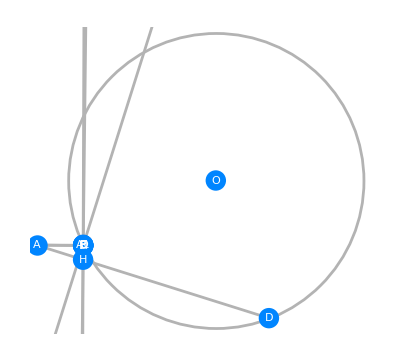

```mathematica
graph003=FindGeometricSceneGraphics[hyp003]
```

```mathematica
thalesCoords=FindGeometricCoordinates@hyp003
```

{GeometricPoint[A]→{-12.3084,5.22919},GeometricPoint[H]→{-10.4734,4.56413},GeometricPoint[D]→{-0.228917,0.851262},GeometricPoint[C]→{-10.4538,5.18357},GeometricPoint[E]→{-10.4577,5.19989},GeometricPoint[B]→{-10.4585,5.17085},GeometricPoint[F]→{-10.4543,5.17072},GeometricPoint[P]→{-10.4581,5.18537},GeometricPoint[Q]→{-10.454,5.17715},GeometricPoint[O]→{-2.83688,8.93436},GeometricPoint[A1]→{-10.4562,5.17721}}

```mathematica
LineThrough[{GeometricPoint["B"],GeometricPoint["D"],GeometricPoint["C"]}]
```

```mathematica
FindGeometricConjectures[graph003]//Column
```

Collinear[GeometricPoint[P],GeometricPoint[C],GeometricPoint[D]]
Similar[Triangle[{GeometricPoint[F],GeometricPoint[A],GeometricPoint[C]}],Triangle[{GeometricPoint[F],GeometricPoint[H],GeometricPoint[B]}]]
Similar[Triangle[{GeometricPoint[F],GeometricPoint[C],GeometricPoint[B]}],Triangle[{GeometricPoint[F],GeometricPoint[A],GeometricPoint[H]}]]
EuclideanDistance[GeometricPoint[H],GeometricPoint[E]]==EuclideanDistance[GeometricPoint[B],GeometricPoint[P]]+EuclideanDistance[GeometricPoint[H],GeometricPoint[P]]
EuclideanDistance[GeometricPoint[H],GeometricPoint[C]]==EuclideanDistance[GeometricPoint[F],GeometricPoint[Q]]+EuclideanDistance[GeometricPoint[H],GeometricPoint[Q]]
EuclideanDistance[GeometricPoint[H],GeometricPoint[P]]==EuclideanDistance[GeometricPoint[H],GeometricPoint[B]]+EuclideanDistance[GeometricPoint[P],GeometricPoint[E]]
EuclideanDistance[GeometricPoint[H],GeometricPoint[Q]]==EuclideanDistance[GeometricPoint[H],GeometricPoint[F]]+EuclideanDistance[GeometricPoint[Q],GeometricPoint[C]]
Angle[GeometricPoint[D],GeometricPoint[H],GeometricPoint[F]]==Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[A1]]
Angle[GeometricPoint[F],GeometricPoint[B],GeometricPoint[P]]==Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[H]]
Angle[GeometricPoint[F],GeometricPoint[B],GeometricPoint[H]]==Angle[GeometricPoint[A],GeometricPoint[B],GeometricPoint[P]]
Angle[GeometricPoint[F],GeometricPoint[B],GeometricPoint[A1]]==Angle[GeometricPoint[A],GeometricPoint[H],GeometricPoint[F]]
Angle[GeometricPoint[P],GeometricPoint[D],GeometricPoint[Q]]==Angle[GeometricPoint[C],GeometricPoint[D],GeometricPoint[Q]]
Angle[GeometricPoint[Q],GeometricPoint[C],GeometricPoint[A1]]==Angle[GeometricPoint[H],GeometricPoint[A],GeometricPoint[B]]
Angle[GeometricPoint[H],GeometricPoint[D],GeometricPoint[P]]==Angle[GeometricPoint[H],GeometricPoint[D],GeometricPoint[C]]
Line[{GeometricPoint[A],GeometricPoint[C]}]⊥LineThrough[{GeometricPoint[H],GeometricPoint[B],GeometricPoint[P],GeometricPoint[E]}]
LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[F]}]⊥LineThrough[{GeometricPoint[H],GeometricPoint[F],GeometricPoint[Q],GeometricPoint[C]}]
LineThrough[{GeometricPoint[A],GeometricPoint[H],GeometricPoint[D]}]⊥LineThrough[{GeometricPoint[B],GeometricPoint[A1],GeometricPoint[C]}]
Angle[GeometricPoint[B],GeometricPoint[F],GeometricPoint[H]]==Angle[GeometricPoint[B],GeometricPoint[F],GeometricPoint[Q]]==90 °

```mathematica
FindGeometricConjectures[graph003,Infinity,"Diagram"]
```

123456789101112131415161718

## Example 004

```mathematica
hyp004={
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["D"]}],
GeometricPoint["S"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["D"]}]],
GeometricPoint["Q"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["S"],GeometricPoint["M"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["Q"],GeometricPoint["M"]}],Line[{GeometricPoint["A"],GeometricPoint["D"]}]],
Collinear[GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["I"]],
Collinear[GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["I"]],
GeometricPoint["J"]==Midpoint[Line[{GeometricPoint["O"],GeometricPoint["M"]}]]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[D]}],GeometricPoint[S]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[D]}]],GeometricPoint[Q]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],Line[{GeometricPoint[S],GeometricPoint[M]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],Line[{GeometricPoint[Q],GeometricPoint[M]}]⊥Line[{GeometricPoint[A],GeometricPoint[D]}],Collinear[GeometricPoint[B],GeometricPoint[C],GeometricPoint[I]],Collinear[GeometricPoint[A],GeometricPoint[D],GeometricPoint[I]],GeometricPoint[J]==Midpoint[Line[{GeometricPoint[O],GeometricPoint[M]}]]}

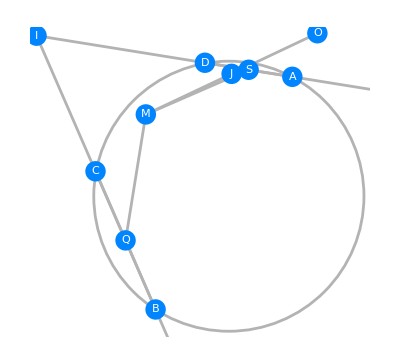

```mathematica
graph004=FindGeometricSceneGraphics[hyp004]
```

```mathematica
thalesCoords=FindGeometricCoordinates@hyp004
```

{A→{2.52675,0.855162},D→{-0.0845446,2.79435},B→{0.706058,1.80049},C→{0.807024,0.208013},GeometricPoint[A]→{1.51054,1.95517},GeometricPoint[B]→{0.3234,2.09567},GeometricPoint[C]→{0.820547,0.341625},GeometricPoint[D]→{0.731009,2.23688},Unspecified[ref,{1,0},1]→{0.58752,0.373073},Unspecified[ref,{1,0},2]→{0.767426,2.24},Unspecified[ref,{1,0},3]→{1.49272,1.97297},Unspecified[ref,{1,0},0]→{0.830142,1.29182},GeometricPoint[S]→{1.2211,1.82476},GeometricPoint[Q]→{0.756541,1.00425}}

```mathematica
FindGeometricConjectures[graph004]//Column
```

EuclideanDistance[GeometricPoint[I],GeometricPoint[B]]==EuclideanDistance[GeometricPoint[C],GeometricPoint[Q]]+EuclideanDistance[GeometricPoint[I],GeometricPoint[Q]]
EuclideanDistance[GeometricPoint[I],GeometricPoint[A]]==EuclideanDistance[GeometricPoint[D],GeometricPoint[S]]+EuclideanDistance[GeometricPoint[I],GeometricPoint[S]]
EuclideanDistance[GeometricPoint[I],GeometricPoint[Q]]==EuclideanDistance[GeometricPoint[I],GeometricPoint[C]]+EuclideanDistance[GeometricPoint[Q],GeometricPoint[B]]
EuclideanDistance[GeometricPoint[I],GeometricPoint[S]]==EuclideanDistance[GeometricPoint[I],GeometricPoint[D]]+EuclideanDistance[GeometricPoint[S],GeometricPoint[A]]
Angle[GeometricPoint[B],GeometricPoint[Q],GeometricPoint[M]]==Angle[GeometricPoint[A],GeometricPoint[S],GeometricPoint[M]]
Angle[GeometricPoint[D],GeometricPoint[S],GeometricPoint[M]]==Angle[GeometricPoint[C],GeometricPoint[Q],GeometricPoint[M]]
LineThrough[{GeometricPoint[I],GeometricPoint[C],GeometricPoint[Q],GeometricPoint[B]}]⊥Line[{GeometricPoint[M],GeometricPoint[S]}]
LineThrough[{GeometricPoint[I],GeometricPoint[D],GeometricPoint[S],GeometricPoint[A]}]⊥Line[{GeometricPoint[Q],GeometricPoint[M]}]

```mathematica
FindGeometricConjectures[graph004,Infinity,"Diagram"]
```

12345678

## Example 005

```mathematica
hyp004={
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["D"]}],
GeometricPoint["S"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["D"]}]],
GeometricPoint["Q"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["S"],GeometricPoint["M"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["Q"],GeometricPoint["M"]}],Line[{GeometricPoint["A"],GeometricPoint["D"]}]],
Collinear[GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["I"]],
Collinear[GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["I"]],
GeometricPoint["J"]==Midpoint[Line[{GeometricPoint["O"],GeometricPoint["M"]}]]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[D]}],GeometricPoint[S]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[D]}]],GeometricPoint[Q]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],Line[{GeometricPoint[S],GeometricPoint[M]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],Line[{GeometricPoint[Q],GeometricPoint[M]}]⊥Line[{GeometricPoint[A],GeometricPoint[D]}],Collinear[GeometricPoint[B],GeometricPoint[C],GeometricPoint[I]],Collinear[GeometricPoint[A],GeometricPoint[D],GeometricPoint[I]],GeometricPoint[J]==Midpoint[Line[{GeometricPoint[O],GeometricPoint[M]}]]}

```mathematica
graph004=FindGeometricSceneGraphics[hyp004]
```

-Graphics-

```mathematica
thalesCoords=FindGeometricCoordinates@hyp004
```

{A→{2.52675,0.855162},D→{-0.0845446,2.79435},B→{0.706058,1.80049},C→{0.807024,0.208013},GeometricPoint[A]→{1.51054,1.95517},GeometricPoint[B]→{0.3234,2.09567},GeometricPoint[C]→{0.820547,0.341625},GeometricPoint[D]→{0.731009,2.23688},Unspecified[ref,{1,0},1]→{0.58752,0.373073},Unspecified[ref,{1,0},2]→{0.767426,2.24},Unspecified[ref,{1,0},3]→{1.49272,1.97297},Unspecified[ref,{1,0},0]→{0.830142,1.29182},GeometricPoint[S]→{1.2211,1.82476},GeometricPoint[Q]→{0.756541,1.00425}}

```mathematica
FindGeometricConjectures[graph004]//Column
```

EuclideanDistance[GeometricPoint[I],GeometricPoint[B]]==EuclideanDistance[GeometricPoint[C],GeometricPoint[Q]]+EuclideanDistance[GeometricPoint[I],GeometricPoint[Q]]
EuclideanDistance[GeometricPoint[I],GeometricPoint[A]]==EuclideanDistance[GeometricPoint[D],GeometricPoint[S]]+EuclideanDistance[GeometricPoint[I],GeometricPoint[S]]
EuclideanDistance[GeometricPoint[I],GeometricPoint[Q]]==EuclideanDistance[GeometricPoint[I],GeometricPoint[C]]+EuclideanDistance[GeometricPoint[Q],GeometricPoint[B]]
EuclideanDistance[GeometricPoint[I],GeometricPoint[S]]==EuclideanDistance[GeometricPoint[I],GeometricPoint[D]]+EuclideanDistance[GeometricPoint[S],GeometricPoint[A]]
Angle[GeometricPoint[B],GeometricPoint[Q],GeometricPoint[M]]==Angle[GeometricPoint[A],GeometricPoint[S],GeometricPoint[M]]
Angle[GeometricPoint[D],GeometricPoint[S],GeometricPoint[M]]==Angle[GeometricPoint[C],GeometricPoint[Q],GeometricPoint[M]]
LineThrough[{GeometricPoint[I],GeometricPoint[C],GeometricPoint[Q],GeometricPoint[B]}]⊥Line[{GeometricPoint[M],GeometricPoint[S]}]
LineThrough[{GeometricPoint[I],GeometricPoint[D],GeometricPoint[S],GeometricPoint[A]}]⊥Line[{GeometricPoint[Q],GeometricPoint[M]}]

```mathematica
FindGeometricConjectures[graph004,Infinity,"Diagram"]
```

12345678

## Example 005

```mathematica
hyp005={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
GeometricPoint["H"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Orthocenter"],
GeometricPoint["O"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Incenter"],
GeometricPoint["A1"]==RegionCenter[Triangle[GeometricPoint/@{"B","C","H"}],"Incenter"]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[H]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Orthocenter],GeometricPoint[O]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Incenter],GeometricPoint[A1]==RegionCenter[Triangle[{GeometricPoint[B],GeometricPoint[C],GeometricPoint[H]}],Incenter]}

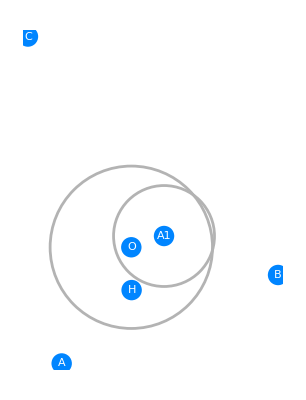

```mathematica
graph005=FindGeometricSceneGraphics[hyp005]
```

```mathematica
thalesCoords=FindGeometricCoordinates@hyp005
```

$Aborted

```mathematica
FindGeometricConjectures[graph005]//Column
```

```mathematica
FindGeometricConjectures[graph005,Infinity,"Diagram"]
```

TabView[{},ControlPlacement→Left]